```mathematica
Quit[]
```

```mathematica
Import["setup/Visual.wl"]
Import["setup/Math.wl"]
Import["Schottky.wl"]
```

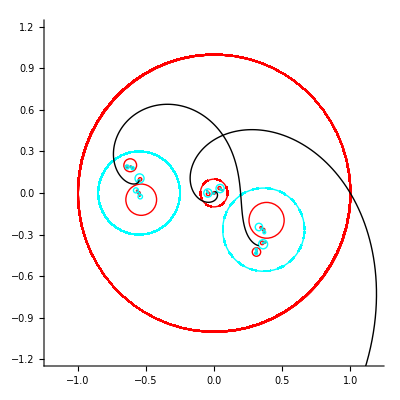

```mathematica
Module[{
c11={0,1},
c12={0,0.1},
c21={-0.55,0.3},
c22={0.45e[0.9],0.3},
c1,c2,C,Γ
},
c1={c11,c12,0.6};
c2={c21,c22,0.7};
C={c1,c2};

Γ=GenerationGetSimpleSchottkyGroup[C];

Graphics[{GraphicsDisplayCover[Γ,5],BranchCutDisplayNormalizedBCycleCurveList[Γ,500,"range"-> {-2,2}]},PlotRange-> GraphicsGetGraphicsRange[Γ],Axes-> True]
]
```

```mathematica
Manipulate[
Module[{
c11={0.7e[1/8],0.4},
c12={0,0.1},
c21={-0.55,0.3},
c22={0.45e[0.9],0.3},
p = x+I y,
c1,c2,C,Γ
},
c1={c11,c12,0.6};
c2={c21,c22,0.7};
C={c1,c2};

Γ=GenerationGetSimpleSchottkyGroup[C];

Graphics[{
GraphicsDisplayCover[Γ,3],
Style[ComplexPoint[#[p]],PointSize[Small]]&/@GroupGetAllMaps[Γ,3],
Style[ComplexPoint[p],Red]
}
,PlotRange-> GraphicsGetGraphicsRange[Γ],Axes-> True]
],
{{x,0.3},-1,1},{{y,0.4},-1,1}
]
```